### Init

```mathematica
n=8;
g=GridGraph[{n,n}];
```

```mathematica
temperatureTable=Table[RandomReal[],n^2];

initialCircleCondition={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

hg1={{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,5},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{11,19},{12,4},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,27},{28,29},{28,36},{29,21},{29,28},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,25},{33,34},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,43},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,54},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,51},{59,58},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}};
```

```mathematica
k=0.1;δt=0.5;
```

```mathematica
ruleSet=ResourceFunction["EnumerateWolframModelRules"][{{2,2}}->{{2,2}}];
```

ResourceObject::updav: There is an update available for resource "ParallelMapMonitored". Use ResourceUpdate[ParallelMapMonitored] to get the update.

```mathematica
graphToHypergraphNew[g_]:=Flatten[DeleteCases[Table[If[(Normal@AdjacencyMatrix@g)[[#]][[i]]*i==0,0,{#,i}],{i,VertexList@g}],0]&/@(VertexList@g),1]

rwLaplacian[g_]:=IdentityMatrix[Length@VertexList@g]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@g],Normal@AdjacencyMatrix[g]]

dynamicDiscreteLaplacian[G_,ϕ_]:=Dot[IdentityMatrix[Length@VertexList@G]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@G],Normal@AdjacencyMatrix[G]],ϕ]

EulerMethod489[{HG_,t_,ϕ_}]:={ResourceFunction["WolframModel"][#,HG,1,"FinalState"]&[ruleSet[[489]]],t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]} 


listEvolution[r_,InitialCondition_]:=NestWhileList[
ResourceFunction["WolframModel"][r,#1,1,"FinalState"]&,
InitialCondition,
(!IsomorphicGraphQ[SimpleGraph@Graph[UndirectedEdge@@@#1],SimpleGraph@Graph[UndirectedEdge@@@#2]]&&ResourceFunction["ConnectedHypergraphQ"][#1])& ,
2,100
]

EulerMethodStatic[{HG_,t_,ϕ_}]:={HG,t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]}
```

```mathematica
gif5=Module[{data=NestList[EulerMethod489,{hg1,0,initialCircleCondition},40]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[1,1]],
GraphLayout->{"GridEmbedding","Dimension"->{8,8}},
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->1,VertexLabels->None,EdgeStyle->Thickness[0]],{i,40}]]
```

## Statistical investigation

We now have a working model of heat transfer on graphs obeying the Wolfram Model rules. The rule 489 is especially interesting, as it leaves the Hausdorff dimension of the graph approximately = 3.

```mathematica
listEvolution[ruleSet[[489]],hg1]
```

{{{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,5},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{11,19},{12,4},156,{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,54},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,51},{59,58},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}},100}
 |  |  |  |

```mathematica
hausdorffDimension489=Module[{rule=ruleSet[[489]]},ResourceFunction["WolframHausdorffDimension"][SimpleGraph[Graph[UndirectedEdge@@@#]],All,{1,1},"VertexMethod"->Mean]&/@listEvolution[rule,hg1]]
```

{2.15514,2.66227,2.89346,2.82673,2.80501,2.78675,2.81704,2.81985,2.82783,2.85418,2.8583,2.84932,2.83344,2.85041,2.86149,2.8829,2.88306,2.89089,2.90695,2.87238,2.87183,2.89252,2.89349,2.8871,2.87888,2.85095,2.89853,2.9198,2.88361,2.93529,2.92743,2.92794,2.90756,2.89573,2.89146,2.92501,2.87818,2.87472,2.89592,2.90511,2.89549,2.8866,2.8624,2.9144,2.9152,2.89083,2.89234,2.91185,2.91719,2.89867,2.90562,2.86673,2.88737,2.86575,2.85316,2.86014,2.87556,2.87825,2.88727,2.89198,2.90731,2.89727,2.90214,2.85357,2.85645,2.88648,2.88745,2.89705,2.88599,2.92391,2.92488,2.90534,2.90213,2.922,2.92311,2.90708,2.89712,2.90053,2.90833,2.93185,2.9207,2.91639,2.91145,2.89167,2.87509,2.88076,2.89556,2.87897,2.89042,2.87587,2.85567,2.89049,2.89205,2.90593,2.89519,2.92046,2.92958,2.90576,2.89096,2.9029,2.86885}

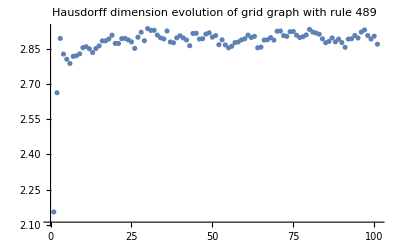

```mathematica
ListPlot[hausdorffDimension489,PlotRange->All,PlotLabel->"Hausdorff dimension evolution of grid graph with rule 489"]
```

```mathematica
p0=Variance/@NestList[EulerMethodStatic,{hg1,0,temperatureTable},100][[All,3]];
```

```mathematica
p489=Variance/@NestList[EulerMethod489,{hg1,0,temperatureTable},100][[All,3]];
```

The fixed graph variance decay is asymptotically hyperbolic, while the rule 489 decay is exponential:

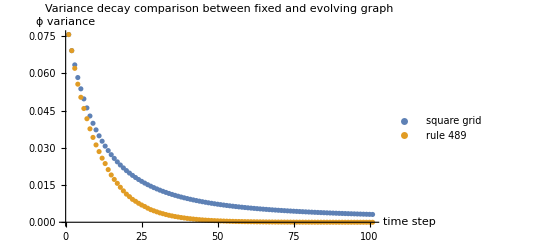

```mathematica
ListPlot[{p0,p489},PlotLabel->"Variance decay comparison between fixed and evolving graph",PlotLegends->{"square grid","rule 489"},PlotRange->All,AxesLabel->{"time step","ϕ variance"}]
```

All of the eigenvalues are non-negative, with one zero value. This value gives the asymptotic behaviour of the system (the average initial temperature at time infinity ).

## Eigenvalue investigation

```mathematica
Re@N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][ResourceFunction["WolframModel"][ruleSet[[489]],hg1,100,"FinalState"]]
```

{1.518,1.45866,1.45866,1.41306,1.41306,1.37605,1.37605,1.40531,1.34593,1.34593,1.368,1.368,1.22436,1.22436,1.26139,1.26139,1.27276,1.23768,1.20016,1.20016,1.12403,1.12403,1.14959,1.14959,1.1022,1.1022,1.05337,1.05337,0.976876,0.976876,0.924589,0.924589,1.00962,1.00962,1.01202,1.01202,0.973808,0.936079,0.936079,0.857672,0.857672,0.918765,0.795133,0.795133,0.843517,0.837009,0.837009,0.745763,0.745763,0.788597,0.788597,0.712223,0.712223,0.612673,0.612673,0.651758,0.621262,0.621262,0.565532,0.565532,0.583195,0.583195,0.48499,0.}

Time series of the Laplacian eigenvalues

```mathematica
hGSeries = NestList[EulerMethod489,{hg1,0,temperatureTable},100]
```

{{1},99,{1}}
 |  |  |  |

```mathematica
eigenSeries = Re@N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][#] & /@ hGSeries[[All, 1]]
```

```mathematica
complexEigenSeries = N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][#] & /@ hGSeries[[All, 1]]
```

{{2.,1.95369,1.95369,1.90097,1.82491,1.82491,1.7635,1.7635,1.64017,1.64017,1.62349,1.56757,1.56757,38,0.432428,0.432428,0.37651,0.359834,0.359834,0.236501,0.236501,0.175093,0.175093,0.0990311,0.0463094,0.0463094,0.},99,{1}}
 |  |  |  |

```mathematica
N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][hGSeries[[10, 1]]]
```

{1.45639+0.168999 ⅈ,1.45639-0.168999 ⅈ,1.45346,1.4126,1.37474+0.307702 ⅈ,1.37474-0.307702 ⅈ,1.32785+0.189125 ⅈ,1.32785-0.189125 ⅈ,1.24224+0.498173 ⅈ,1.24224-0.498173 ⅈ,1.29973+0.283772 ⅈ,1.29973-0.283772 ⅈ,1.25807+0.401021 ⅈ,1.25807-0.401021 ⅈ,1.29744+0.19115 ⅈ,1.29744-0.19115 ⅈ,1.27056+0.0605269 ⅈ,1.27056-0.0605269 ⅈ,1.20023+0.129348 ⅈ,1.20023-0.129348 ⅈ,1.1496+0.323863 ⅈ,1.1496-0.323863 ⅈ,1.13763+0.239806 ⅈ,1.13763-0.239806 ⅈ,1.08123+0.406029 ⅈ,1.08123-0.406029 ⅈ,1.14686,1.05313+0.44963 ⅈ,1.05313-0.44963 ⅈ,0.94806+0.392256 ⅈ,0.94806-0.392256 ⅈ,1.01109+0.167183 ⅈ,1.01109-0.167183 ⅈ,0.905665+0.458975 ⅈ,0.905665-0.458975 ⅈ,0.970389+0.248182 ⅈ,0.970389-0.248182 ⅈ,0.991276,0.909729+0.0914536 ⅈ,0.909729-0.0914536 ⅈ,0.913036,0.836922+0.272105 ⅈ,0.836922-0.272105 ⅈ,0.856202,0.726284+0.372631 ⅈ,0.726284-0.372631 ⅈ,0.748702+0.252112 ⅈ,0.748702-0.252112 ⅈ,0.743028+0.105636 ⅈ,0.743028-0.105636 ⅈ,0.683493+0.233104 ⅈ,0.683493-0.233104 ⅈ,0.644944+0.279383 ⅈ,0.644944-0.279383 ⅈ,0.648808+0.0552139 ⅈ,0.648808-0.0552139 ⅈ,0.573918+0.260188 ⅈ,0.573918-0.260188 ⅈ,0.575452,0.495949+0.0877418 ⅈ,0.495949-0.0877418 ⅈ,0.480018,0.34612,0.}

```mathematica
complexEigenSeries[[All,2]][[1;;10]]
```

{1.95369,1.44867-0.755046 ⅈ,1.38418-0.531425 ⅈ,1.56259-0.297944 ⅈ,1.4752,1.49113-0.331725 ⅈ,1.4831-0.121362 ⅈ,1.52324+0.118829 ⅈ,1.48731+0.1202 ⅈ,1.45639-0.168999 ⅈ}

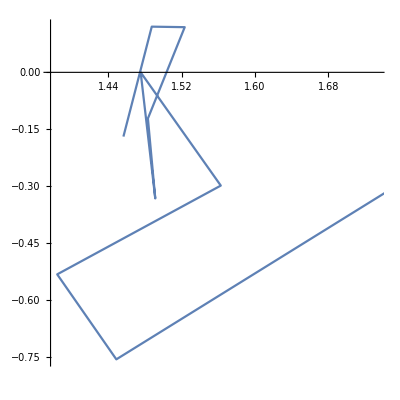

```mathematica
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%88,AspectRatio->1]
```

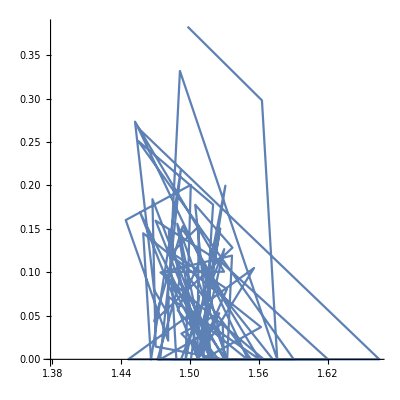

```mathematica
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%79,AspectRatio->1]
```

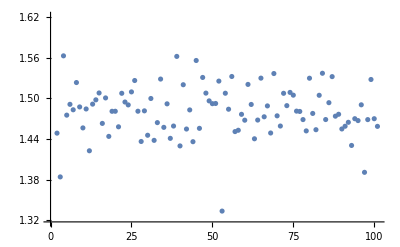

```mathematica
ListPlot[%75]
```

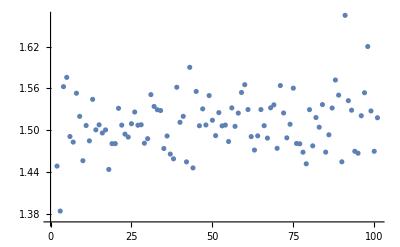

```mathematica
ListPlot[%73]
```